```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-7;
L=100000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.2;x0=1/(2 2 h s N1);
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1500}];

tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1500},{x,0,1}];
gData=Table[ G[x,tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];


averageGData={};
AppendTo[averageGData,gData];
xaxish2=Table[x,{x,0.001,0.999,0.001}];

Datah2=Transpose@{xaxish2,xaxish2 gData/theta};
```

275.295

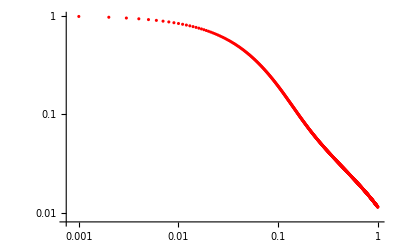

```mathematica
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

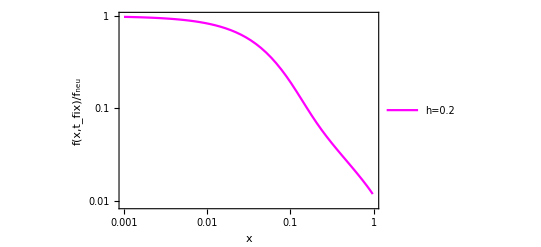

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}, PlotMarkers->{"▲",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```